# Knowledge Representation in the Wolfram Language

See “Knowledge Representation & Access” in the Wolfram Language Guide

## Wolfram Language Data

The Wolfram Language itself is knowledge represented in the Wolfram Language:

```mathematica
WolframLanguageData["Classes"]
```

{Wolfram Language experimental symbols,Wolfram Language atomic functions,Wolfram Language autoevaluating symbols,Wolfram Language curryable symbols,all Wolfram Language symbols}

Our WolframLanguageData input appears to be identical to this EntityClassList input:

```mathematica
EntityClassList["WolframLanguageSymbol"]
```

{Wolfram Language experimental symbols,Wolfram Language atomic functions,Wolfram Language autoevaluating symbols,Wolfram Language curryable symbols,all Wolfram Language symbols}

The output are instances of EntityClass. Let’s see a Shallow list of Wolfram Language experimental symbols:

```mathematica
EntityList[EntityClass["WolframLanguageSymbol","Experimental"]]//Shallow
```

{AnatomyForm,AnatomyPlot3D,Ask,AskAppend,AskConfirm,AskDisplay,AskedQ,AskedValue,AskFunction,AskTemplateDisplay,«111»}

Use Dataset to scroll/browse through all of the symbols:

```mathematica
Dataset[EntityList[EntityClass["WolframLanguageSymbol","Experimental"]]]
```

Dataset[<>]

Use Select to target a subset:

```mathematica
Select[
EntityList[EntityClass["WolframLanguageSymbol","Experimental"]],StringMatchQ[EntityValue[#,EntityProperty["WolframLanguageSymbol","Name"]],"Feature*"]&
]
```

{FeatureDistance,FeatureExtract,FeatureExtraction,FeatureExtractor,FeatureExtractorFunction}

```mathematica
EntityProperties[Entity["WolframLanguageSymbol","AnatomyForm"]]
```

{attributes,common option values,date introduced,date last modified,dates modified,documentation basic examples,documentation example counts,documentation example inputs,documentation example text,eponymous people,equal-precedence symbols,external links,frequencies of usage,full version introduced,full version last modified,full versions modified,functionality areas,symbol background,keyboard shortcuts,link trails,memberships,name,option names,options,plaintext usage,precedence ranks,ranks of usage,related entities,related symbols,relationship community graph,relationship graph,short notations,subject classifications,text strings,timeline,translations,typeset usage,URL,version introduced,version last modified,versions modified}

We see from the EntityProperties of the AnatomyForm Entity date-related properties that suggest that a TimelinePlot can be generated:

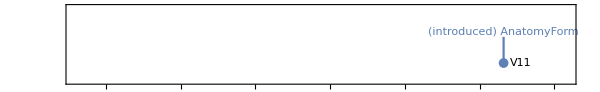

```mathematica
WolframLanguageData[Entity["WolframLanguageSymbol","AnatomyForm"],"Timeline"]
```

EntityValue from an EntityProperty:

```mathematica
EntityValue[Entity["WolframLanguageSymbol","AnatomyForm"],EntityProperty["WolframLanguageSymbol","PlaintextUsage"]]
```

AnatomyForm[g] is a graphics directive used in AnatomyPlot3D that specifies how anatomy entity-based graphics objects are to be drawn using the graphics directive or association of directives g.

```mathematica
EntityValue[Entity["WolframLanguageSymbol","AnatomyForm"],EntityProperty["WolframLanguageSymbol","RelatedSymbols"]]
```

{AnatomyPlot3D,AnatomyData,HumanGrowthData,EntityValue}

We see that EntityValue is an explicit form of this equivalent expression:

```mathematica
Entity["WolframLanguageSymbol","AnatomyForm"][EntityProperty["WolframLanguageSymbol","RelatedSymbols"]]
```

{AnatomyPlot3D,AnatomyData,HumanGrowthData,EntityValue}

Or the Input Text form:

```mathematica
Entity["WolframLanguageSymbol","AnatomyForm"]["RelatedSymbols"]
```

{AnatomyPlot3D,AnatomyData,HumanGrowthData,EntityValue}